## Step 2.1

### Behavior of the cdf of the binomial

```mathematica
foo=Table[Probability[Z≥3,Z\[Distributed]BinomialDistribution[δ,(M-1)/M]],{δ,5,15}]
```

{((-1+M)^3 (6+3 M+M^2))/M^5,((-1+M)^3 (10+6 M+3 M^2+M^3))/M^6,((-1+M)^3 (15+10 M+6 M^2+3 M^3+M^4))/M^7,((-1+M)^3 (21+15 M+10 M^2+6 M^3+3 M^4+M^5))/M^8,((-1+M)^3 (28+21 M+15 M^2+10 M^3+6 M^4+3 M^5+M^6))/M^9,((-1+M)^3 (36+28 M+21 M^2+15 M^3+10 M^4+6 M^5+3 M^6+M^7))/M^10,((-1+M)^3 (45+36 M+28 M^2+21 M^3+15 M^4+10 M^5+6 M^6+3 M^7+M^8))/M^11,BetaRegularized[(-1+M)/M,3,10],BetaRegularized[(-1+M)/M,3,11],BetaRegularized[(-1+M)/M,3,12],BetaRegularized[(-1+M)/M,3,13]}

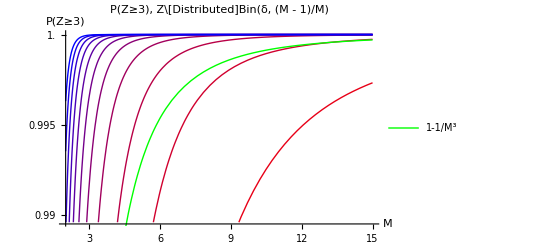

```mathematica
Show[{
Plot[foo,{M,2,15},
PlotStyle->Table[Blend[{Red,Blue},δ/11],{δ,1,11}],
PlotLegends->legend],
Plot[1-1/M^3,{M,2,15},
PlotStyle->{Thick,Green},
PlotLegends->Placed["Expressions",{Right,Bottom}]]
},
PlotLabel->"P(Z≥3), Z\[Distributed]Bin(δ, (M - 1)/M)",
LabelStyle->Directive[FontFamily->"Helvetica"],
AxesLabel->{"M","P(Z≥3)"},
Ticks->{Automatic,{0.99,0.995,1.0}}
]
```

### Derivative of the binomial

```mathematica
f[n_]:=Sum[Binomial[n,k]p^k(1-p)^(n-k),{k,0,2}]
```

```mathematica
D[Binomial[n,k]p^k(1-p)^(n-k),n]/.Binomial->bin//FunctionExpand//Simplify
```

(1-p)^(-k+n) p^k bin[n,k] (Log[1-p]+PolyGamma[0,1+n]-PolyGamma[0,1-k+n])

```mathematica
FunctionExpand[D[Binomial[n,k],n],Assumptions->{n∈Integers,k∈Integers,n>k>0}]//FullSimplify
```

(Gamma[1+n] (HarmonicNumber[n]-HarmonicNumber[-k+n]))/(Gamma[1+k] Gamma[1-k+n])

### Hoeffding

```mathematica
Exp[-2δ((M-1)/M-2/δ)^2]
```

ⅇ^(-2 ((-1+M)/M-2/δ)^2 δ)

```mathematica
Manipulate[
Plot[{ⅇ^(-2 ((-1+M)/M-2/δ)^2 δ),1/M^3},
{M,4,500}],
 {δ,6,50},ControlType->Slider
]
```

```mathematica
Limit[#,M->Infinity]&/@Table[(ⅇ^(-2 ((-1+M)/M-2/δ)^2 δ))/(1/M^3),{δ,Range[3,15]}]
```

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
Limit[(ⅇ^(-2 ((-1+M)/M-2/δ)^2 δ)),M->Infinity]
```

ⅇ^(-(2 (-2+δ)^2)/δ)

### Play

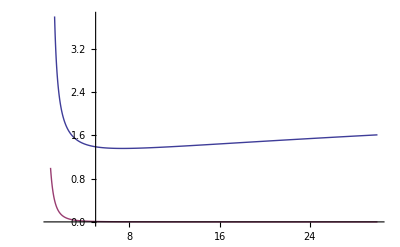

```mathematica
Plot[{Sqrt@x/Log[x],1/x^3},{x,1,30}]
```

## Step 2.2

```mathematica
Sum[3^m,{m,0,j-1}]
```

1/2 (-1+3^j)

```mathematica
Sum[3^m,{m,0,j-2}]
```

1/6 (-3+3^j)

```mathematica
Sum[(δ^m)/Factorial@m,{m,0,lim}](*/.lim->Ceiling[1/2 (-1+δ √M)]*)//FunctionExpand
```

(ⅇ^δ Gamma[1+lim,δ])/Gamma[1+lim]

```mathematica
Sum[(δ^m)/Factorial@m,{m,0,lim}]/.lim->Ceiling[1/2 (-1+δ √M)]
```

(ⅇ^δ Gamma[1+Ceiling[1/2 (-1+√M δ)],δ])/(Ceiling[1/2 (-1+√M δ)]!)

```mathematica
Table[(ⅇ^δ Gamma[1+Ceiling[1/2 (-1+√M δ)],δ])/(Ceiling[1/2 (-1+√M δ)]!),{δ,6,10}]//FunctionExpand//FullSimplify
```

{(ⅇ^6 Gamma[1+Ceiling[-1/2+3 √M],6])/Gamma[1+Ceiling[-1/2+3 √M]],(ⅇ^7 Gamma[1+Ceiling[1/2 (-1+7 √M)],7])/Gamma[1+Ceiling[1/2 (-1+7 √M)]],(ⅇ^8 Gamma[1+Ceiling[-1/2+4 √M],8])/Gamma[1+Ceiling[-1/2+4 √M]],(ⅇ^9 Gamma[1+Ceiling[1/2 (-1+9 √M)],9])/Gamma[1+Ceiling[1/2 (-1+9 √M)]],(ⅇ^10 Gamma[1+Ceiling[-1/2+5 √M],10])/Gamma[1+Ceiling[-1/2+5 √M]]}

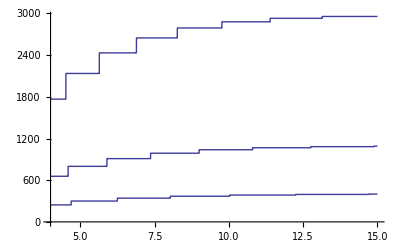

```mathematica
Plot[Table[(ⅇ^δ Gamma[1+Ceiling[1/2 (-1+√M δ)],δ])/(Ceiling[1/2 (-1+√M δ)]!),{δ,6,10}]⟦;;3⟧,{M,4,15}]
```

```mathematica
Sum[δ^(δ Sqrt@M-k),{k,(δ Sqrt@M+1)/2,δ Sqrt@M}]//FullSimplify
```

(-1+δ^(1/2 (1+√M δ)))/(-1+δ)

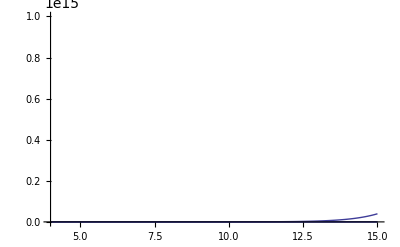

```mathematica
Plot[Table[(-1+δ^(1/2 (1+√M δ)))/(-1+δ),{δ,6,15}],{M,4,15}]
```

```mathematica
Sum[δ^m,{m,F/2,F}]//Simplify
```

(-δ^(F/2)+δ^(1+F))/(-1+δ)

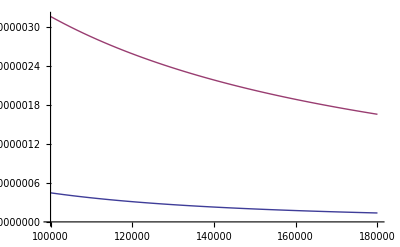

```mathematica
Plot[{(Sqrt@M)/(5Log[M]!),1/M^1.1},{M,100000,180000}]
```

```mathematica
FullSimplify[(Sqrt@M)/(5Log[M]!)>1/M^3,Assumptions->{M>0,M∈Integers}]
```

M^(7/2)>5 Gamma[1+Log[M]]

```mathematica
Plot[{Sqrt@M/(Log@M)!,1/M^3},{M,350000000000000000000000000000000000000,500000000000000000000000000000000000}]
```

-Graphics-

```mathematica
Plot[{(2Log@M)^10/M^4,1/M^3},{M,30000000000000000000,50000000000000000000}]
```

-Graphics-

```mathematica
δ Sum[3^m,{m,0,j-2}]+(δ(3^(j-1))-1)/(2(δ-1))//Simplify
```

(-3+3 δ+(-3+3^j) δ^2)/(6 (-1+δ))

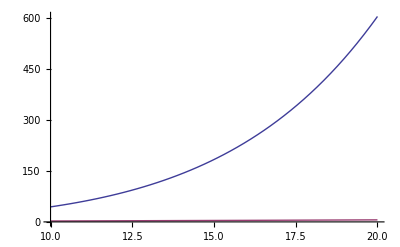

```mathematica
Plot[{Sqrt@M Log[M]^Sqrt@M,Factorial[Log[M]]},{M,10,20}]
```

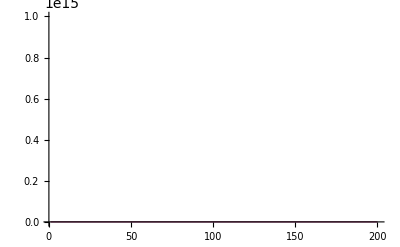

```mathematica
Plot[{6^(6 Sqrt@M+1),5Factorial[Log[M]]},{M,1,200}]
```

```mathematica
Sum[δ^m,{m,δ Sqrt[M]/2,δ Sqrt[M]}]//FullSimplify
```

(-δ^((√M δ)/2)+δ^(1+√M δ))/(-1+δ)

```mathematica
Sum[δ^m,{m,0,T}]//FullSimplify
```

(-1+δ^(1+T))/(-1+δ)

```mathematica
(-1+δ^(1+T))/(-1+δ)//Expand
```

-1/(-1+δ)+δ^(1+T)/(-1+δ)

```mathematica
Solve[Log[Sqrt[x]/E]==Log[x^α],α]
```

{{α→(-2+Log[x])/(2 Log[x])}}

```mathematica
(*Solve[{3^(j-1)≤(2(δ^τ-1))/(δ-1)+1,3^(τ-1)≤2δ^j+1},{j,τ}]*)
```

```mathematica
bar=And@@@Table[{3^(j-1)≤(2(δ^τ-1))/(δ-1)+1,3^(τ-1)≤2δ^j+1},{δ,6,30}];
```

```mathematica
bar⟦1⟧
```

3^(-1+j)≤1+2/5 (-1+6^τ)&&3^(-1+τ)≤1+2^(1+j) 3^j

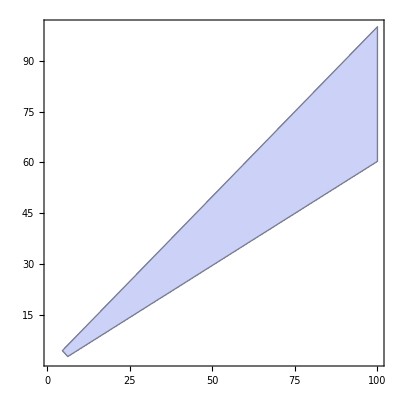

```mathematica
RegionPlot[bar⟦1⟧&&j≤τ,{τ,1,100},{j,2,100}]
```

```mathematica
Sum[(δ^j/Sqrt@M)^m,{m,r/2,r}]//FullSimplify
```

(√M (δ^j/(√M))^(r/2)-δ^j (δ^j/(√M))^r)/(√M-δ^j)

```mathematica
Sum[M^(μ(3-δ/2)),{μ,3^(j-1),δ^(j-1)}]
```

(M^(δ/2) (M^(3^(-1+j) (3-δ/2))-M^((3-δ/2) (1+δ^(-1+j)))))/(-M^3+M^(δ/2))

```mathematica
Sum[M^(μ(3-δ/2)),{μ,0,Infinity}]
```

M^(δ/2)/(-M^3+M^(δ/2))

```mathematica
M^(δ/2)/(-M^3+M^(δ/2))<1//Simplify
```

M^(1+δ/2)<M^4

```mathematica
Sum[4^(δ μ)M^(3μ-1-δ μ/2),{μ,3^(j-1),δ^(j-1)}]
```

-(M^(-1+δ/2-1/2 3^(-1+j) δ-1/2 δ (1+δ^(-1+j))) (4^(δ (1+δ^(-1+j))) M^(3+1/2 3^(-1+j) δ+3 δ^(-1+j))-4^(3^(-1+j) δ) M^(3^j+1/2 δ (1+δ^(-1+j)))))/(-4^δ M^3+M^(δ/2))

```mathematica
-1/(-4^δ M^3+M^(δ/2))M^(-1+δ/2-1/2 3^(-1+j) δ-1/2 δ (1+δ^(-1+j))) (4^(δ (1+δ^(-1+j))) M^(3+1/2 3^(-1+j) δ+3 δ^(-1+j))-4^(3^(-1+j) δ) M^(3^j+1/2 δ (1+δ^(-1+j))))//FullSimplify
```

-(4^(3^(-1+j) δ) M^(-1+3^j-1/6 (-3+3^j) δ)-4^(δ+δ^j) M^(2-1/2 (-6+δ) δ^(-1+j)))/(4^δ M^3-M^(δ/2))

```mathematica
3^(j-1)(δ/2-3)+1-j+1≥3//FullSimplify
```

3^j (-6+δ)≥6+6 j

```mathematica
FullSimplify[3^(j-1)(δ/2-3)+1-j+1≥3,Assumptions->{δ>6,j≥2}]
```

3^j (-6+δ)≥6+6 j

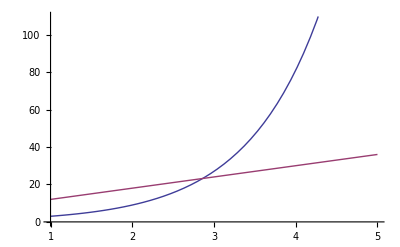

```mathematica
Plot[{3^j ,6+6 j},{j,1,5}]
```

## Step 2.4

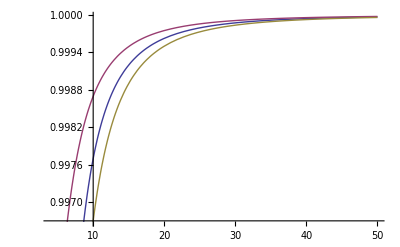

```mathematica
Plot[Tooltip@{(1-1/M^3)^Log[M],(1-1/M^3)^(Log[M]-1),(1-1/M^3)^(Log[M]+1)},{M,4,50}]
```

```mathematica
Sum[E^j,{j,1,τ-1}]
```

(-ⅇ+ⅇ^τ)/(-1+ⅇ)

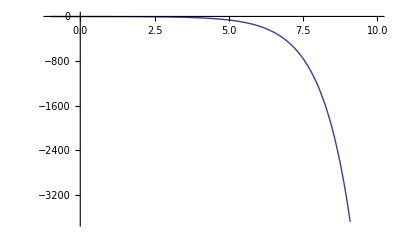

```mathematica
Plot[(-ⅇ+ⅇ^τ)/(-1+ⅇ)-E^τ,{τ,-1,10}]
```

```mathematica
Log[M/2]//FunctionExpand
```

-Log[2]+Log[M]

```mathematica
Log[2]//N
```

0.693147

```mathematica
Log[3,2]//N
```

0.63093

```mathematica
Table[N@E^i,{i,1,10}]
```

{2.71828,7.38906,20.0855,54.5982,148.413,403.429,1096.63,2980.96,8103.08,22026.5}

```mathematica
N@E^9
```

8103.08

```mathematica
M=16208;
L=10;
```

```mathematica
E^(L-1)<M/2<E^L
```

True

```mathematica
E^(L-1)<M<E^L
```

True

```mathematica
L-1<Log@M<L
```

True

## Step 4

```mathematica
(2Log[N/δ]+2)/(N/δ)^3-(Log[N/δ]+1)^2/(N/δ)^6//FullSimplify
```

-((1+Log[N/δ]) (-2 N^3 δ^3+δ^6+δ^6 Log[N/δ]))/N^6

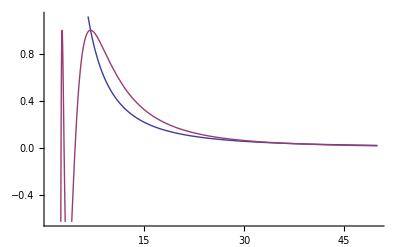

```mathematica
Plot[{1/(N/δ)^2/.δ->7,(2Log[N/δ]+2)/(N/δ)^3-(Log[N/δ]+1)^2/(N/δ)^6/.δ->7},{N,1,50}]
```

```mathematica
Sum[1/(M)^2,{M,1,Infinity}]/.M->N/δ
```

π^2/6